```mathematica
Remove["Global`*"]
```

```mathematica
Reduce[Subscript[x, 1]^Subscript[a, 1]*Subscript[x, 2]^Subscript[a, 2]/.Solve[{p*Subscript[a, 1]*Subscript[x, 1]^(Subscript[a, 1]-1)*Subscript[x, 2]^Subscript[a, 2]==Subscript[w, 1],p*Subscript[a, 2]*Subscript[x, 1]^Subscript[a, 1]*Subscript[x, 2]^(Subscript[a, 2]-1)==Subscript[w, 2]},{Subscript[x, 1],Subscript[x, 2]}],{Subscript[a, 1],Subscript[a, 2]}]
```

Reduce::naqs: (ⅇ^-Log[p] - Log[Subscript[« 2 »]] + « 4 » + Log[Subscript[« 2 »]]\ « 1 » - Log[Subscript[« 2 »]]\ a_1/-1 + a_1 + a_2)^a_2\ (ⅇ^« 9 » + Log[Subscript[« 2 »]]\ a_2/-1 + a_1 + a_2)^a_1 is not a quantified system of equations and inequalities.

Reduce[{(ⅇ^((-Log[p]-Log[a_2]+Log[w_2]-Log[a_1] a_1+Log[a_2] a_1+Log[w_1] a_1-Log[w_2] a_1)/(-1+a_1+a_2)))^a_2 (ⅇ^((-Log[p]-Log[a_1]+Log[w_1]+Log[a_1] a_2-Log[a_2] a_2-Log[w_1] a_2+Log[w_2] a_2)/(-1+a_1+a_2)))^a_1},{a_1,a_2}]

```mathematica
Simplify[1/(Subscript[a, 1]+Subscript[a, 2])*((Subscript[a, 1]/Subscript[a, 2])^Subscript[a, 2]+(Subscript[a, 2]/Subscript[a, 1])^Subscript[a, 1])^(1/(Subscript[a, 1]+Subscript[a, 2])),{Subscript[a, 1],Subscript[a, 2]}]
```

2^(-1+1/(2 True))/True

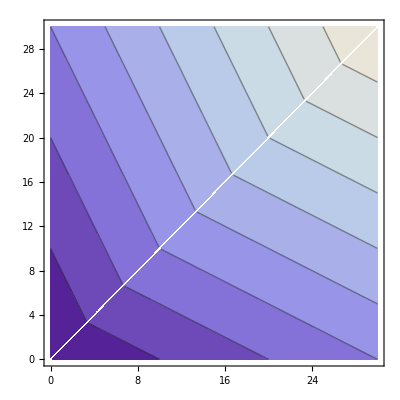

Plot::nonopt: Options expected (instead of {x_2, 0, 3}) beyond position 2 in Plot[Min[2\ x_1 + x_2, 2\ x_2 + x_1] == 4, {x_1, 0, 3}, {x_2, 0, 3}]. An option must be a rule or a list of rules.

Plot::nonopt: Options expected (instead of {x2, 0, 3}) beyond position 2 in Plot[Min[2\ x_1 + x_2, 2\ x_2 + x_1] == 4, {x_1, 0, 3}, {x2, 0, 3}]. An option must be a rule or a list of rules.

Plot[Min[2 x_1+x_2,2 x_2+x_1]==4,{x_1,0,3},{x2,0,3}]

```mathematica
ContourPlot[Min[2*Subscript[x, 1]+Subscript[x, 2],2*Subscript[x, 2]+Subscript[x, 1]],{Subscript[x, 1],0,30},{Subscript[x, 2],0,30}]
```